```mathematica
find[n_]:=1/Sqrt[1/n^2-(5.87433*10^-6)/13.605693]
```

```mathematica
close[n_]:=(13.605693/(5.87433*10^-6)#-1)&/@{1/n^2-1/Floor[find[n]]^2,1/n^2-1/Ceiling[find[n]]^2}
```

```mathematica
NN=21.1061140542/9.1126705055349*^-6;
e=1/NN;
```

```mathematica
Sqrt[NN]
```

1521.88

```mathematica
upper=(1+10^-6)e;
lower=(1-10^-6)e;
```

```mathematica
findall[n_]:={#->n,10^9(N[1/n^2-1/#^2]/e-1)}&/@Range[Ceiling[1/Sqrt[1/n^2-lower]],Floor[1/Sqrt[1/n^2-upper]]]
```

```mathematica
SortBy[Join@@findall/@Range[1521],#[[2]]&]//TableForm
```

44634→1521 | -998.446
30558→1520 | -994.22
24686→1519 | -969.547
44635→1521 | -946.352
17257→1516 | -894.475
44636→1521 | -894.263
44637→1521 | -842.177
18951→1517 | -832.589
30559→1520 | -831.891
44638→1521 | -790.094
44639→1521 | -738.015
1651→1119 | -702.196
44640→1521 | -685.939
21262→1518 | -680.157
1607→1105 | -676.882
30560→1520 | -669.577
12657→1511 | -664.793
24687→1519 | -661.644
44641→1521 | -633.867
44642→1521 | -581.798
44643→1521 | -529.733
30561→1520 | -507.28
44644→1521 | -477.672
44645→1521 | -425.613
5409→1465 | -379.768
44646→1521 | -373.559
24688→1519 | -353.779
30562→1520 | -344.999
44647→1521 | -321.508
15947→1515 | -314.965
44648→1521 | -269.46
44649→1521 | -217.416
21263→1518 | -198.265
30563→1520 | -182.733
14894→1514 | -173.357
44650→1521 | -165.375
10802→1507 | -164.548
18952→1517 | -152.036
5460→1466 | -149.688
4541→1443 | -125.368
44651→1521 | -113.338
44652→1521 | -61.3044
24689→1519 | -45.9503
30564→1520 | -20.4839
44653→1521 | -9.27418
17258→1516 | 6.8029
12107→1510 | 13.0107
44654→1521 | 42.7525
44655→1521 | 94.7757
30565→1520 | 141.75
44656→1521 | 146.795
10132→1505 | 192.32
44657→1521 | 198.812
44658→1521 | 250.824
24690→1519 | 261.841
21264→1518 | 283.559
44659→1521 | 302.833
30566→1520 | 303.967
14024→1513 | 324.375
44660→1521 | 354.839
11190→1508 | 364.227
13289→1512 | 372.482
44661→1521 | 406.841
3587→1401 | 441.543
44662→1521 | 458.84
11622→1509 | 460.7
30567→1520 | 466.169
44663→1521 | 510.835
18953→1517 | 528.409
44664→1521 | 562.827
24691→1519 | 569.594
44665→1521 | 614.815
8489→1498 | 624.87
30568→1520 | 628.355
44666→1521 | 666.8
44667→1521 | 718.781
3905→1418 | 751.989
21265→1518 | 765.315
44668→1521 | 770.759
9092→1501 | 779.146
30569→1520 | 790.525
44669→1521 | 822.733
15948→1515 | 827.163
44670→1521 | 874.704
24692→1519 | 877.31
17259→1516 | 907.925
44671→1521 | 926.672
30570→1520 | 952.679
44672→1521 | 978.635
9571→1503 | 986.304

```mathematica
SortBy[Join@@findall/@Range[1000],#[[2]]&]//TableForm
```

```mathematica
findraw[n_]:=Range[Ceiling[1/Sqrt[1/n^2-lower]],Floor[1/Sqrt[1/n^2-upper]]]
```

```mathematica
findcm[n_]:={#->n,9.1126705055349*^-6/(1/n^2-1/#^2)}&/@findraw[n]
```

```mathematica
SortBy[Join@@findcm/@Range[1000],#[[2]]&]//TableForm
```

1151→918 | 21.104
1315→995 | 21.1048
1118→901 | 21.1049
1183→934 | 21.1052
1086→884 | 21.1053
1030→853 | 21.1054
1016→845 | 21.1059
1149→917 | 21.106
829→728 | 21.1061
616→571 | 21.1065
446→428 | 21.1066
1216→950 | 21.1067
1261→971 | 21.1068
1185→935 | 21.1072
1272→976 | 21.1072
727→656 | 21.1077

```mathematica
upper=(1+10^-4)e;
lower=(1-10^-4)e;
```

```mathematica
findtext[n_]:=Text[#->n,{n/200,10^3(9.1126705055349*^-6/(1/n^2-1/#^2)-21.1)}]&/@findraw[n]
```

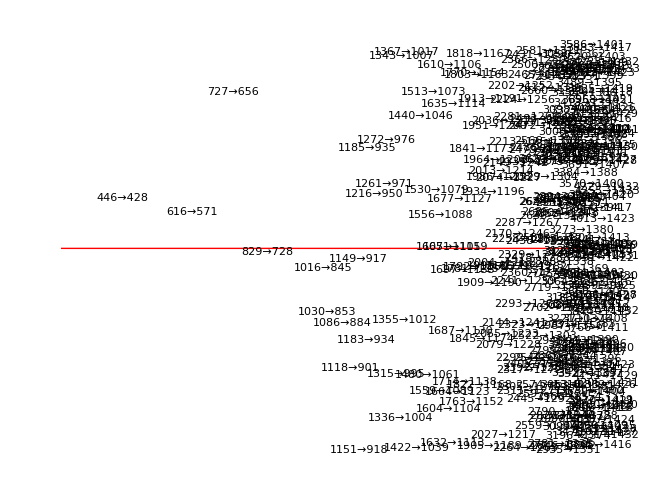

```mathematica
Graphics[(Join@@findtext/@Range[1521])~Join~{Red,Line[{{1.5,6.1140542},{7,6.1140542}}]}~Join~Table[Text[21.1+10^-3n,{1.5,n}],{n,4,8}]]
```

```mathematica
upper=1.005e;
lower=.995e;
```

```mathematica
findtext[n_]:=Text[#->n,{n/30,100*(9.1126705055349*^-6/(1/n^2-1/#^2)-21)}]&/@findraw[n]
```

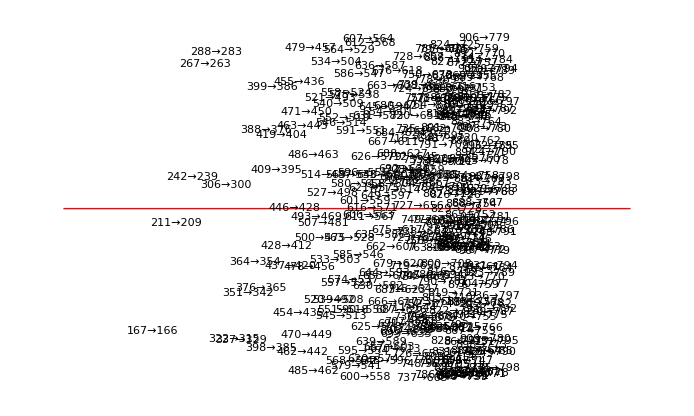

```mathematica
Graphics[(Join@@findtext/@Range[999])~Join~{Red,Line[{{0,100*.1061140542},{35,100*.1061140542}}]}~Join~Table[Text[21+.1n,{0,10n}],{n,0,2}]]
```

```mathematica
e
```

4.31755×10^-7

```mathematica
(1/165^2-1/166^2)/e
```

1.0219

```mathematica
Join@@findtext/@Range[800]//N
```

```mathematica
findtext[n_]:=Text[DisplayForm@SubscriptBox[n,#-n],{n/30,100*(9.1126705055349*^-6/(1/n^2-1/#^2)-21)}]&/@findraw[n]
```

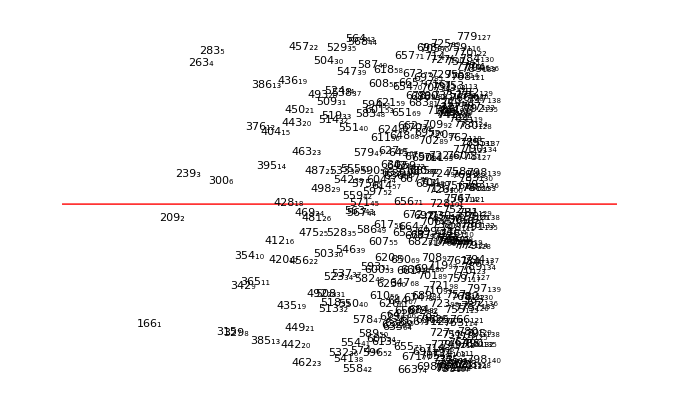

```mathematica
Graphics[(Join@@findtext/@Range[999])~Join~{Red,Line[{{0,100*.1061140542},{35,100*.1061140542}}]}~Join~Table[Text[21+.1n,{0,10n}],{n,0,2}]]
```

```mathematica
H166α
H209β
H239γ
H263δ
H283ϵ
H300ζ

H428σ

H469ω
```